## Lesson 22: Solution of initial value problems

## Overview

This lesson will discuss how a Laplace transform can be used to solve differential equations.

The Laplace transform of the derivative can be expressed as the transform of the original function in quite simple terms:

```mathematica
LaplaceTransform[f'[t],t,s]
```

-f[0]+s LaplaceTransform[f[t],t,s]

Thus, through the use of the Laplace transform, the differential equation can be transformed into a polynomial equation that is much easier to solve.

## Laplace Transform of Derivatives

The transform of the derivative can quite simply be expressed in terms of the transform of the original function:

```mathematica
LaplaceTransform[f'[t],t,s]
```

-f[0]+s LaplaceTransform[f[t],t,s]

This property extends to any degree of differentiation:

```mathematica
LaplaceTransform[f''[t],t,s]
```

-s f[0]+s^2 LaplaceTransform[f[t],t,s]-f'[0]

In fact, there is a general formula for expressing the Laplace transform of the n^th derivative:

L{f^(n)(t)}=s^n L{f(t)}-s^(n-1)f(0)-...-s f^(n-2)(0)-f^(n-1)(0)

```mathematica
LaplaceTransform[D[f[t],{t,5}],t,s]
```

-s^4 f[0]+s^5 LaplaceTransform[f[t],t,s]-s^3 f'[0]-s^2 f''[0]-s f^(3)[0]-f^(4)[0]

## Example 1: Homogeneous Equation

Consider the differential equation:

y''(x)+y(x)=0

combined with the initial conditions:

y(0)=1

y'(0)=0

Define this equation in the Wolfram Language:

```mathematica
eqn=y''[t]+y[t]==0
```

y[t]+y''[t]==0

Utilize the function LaplaceTransform to transform the entire equation:

```mathematica
LaplaceTransform[eqn, t,s]
```

LaplaceTransform[y[t],t,s]+s^2 LaplaceTransform[y[t],t,s]-s y[0]-y'[0]==0

## Example 1: Homogeneous Equation

Next, replace the corresponding initial values in the equation to obtain the following:

```mathematica
leqn = LaplaceTransform[eqn, t,s]/.{y[0]->1,y'[0]->0}
```

-s+LaplaceTransform[y[t],t,s]+s^2 LaplaceTransform[y[t],t,s]==0

Solve for L{y(t)} to obtain the following equation:

```mathematica
Solve[leqn,LaplaceTransform[y[t],t,s]]
```

{{LaplaceTransform[y[t],t,s]→s/(1+s^2)}}

What you have found is that the solution to the initial value problem is the function that has the Laplace transform of:

F(s)=s/(1+s^2)

You can actually find out exactly what the unknown function is using InverseLaplaceTransform.

## Example 1: Homogeneous Equation

Calculate the inverse of the Laplace transform of the solution to obtain y(t):

```mathematica
InverseLaplaceTransform[s/(1+s^2),s,t]
```

Cos[t]

You can confirm this result with the function DSolveValue:

```mathematica
DSolveValue[{y''[t]+y[t]==0,y[0]==1,y'[0]==0},y[t],t]
```

Cos[t]

Thus you have solved the initial value problem only using the Laplace transform and its associated properties.

## Example 2: Nonhomogeneous Equation

Consider the differential equation:

y''(t)+y(t)=cos(2 t)

combined with the initial conditions:

y(0)=1

y'(0)=0

Define this equation in the Wolfram Language:

```mathematica
eqn=y''[t]+y[t]==Cos[2t]
```

y[t]+y''[t]==Cos[2 t]

Use LaplaceTransform to transform the entire equation:

```mathematica
LaplaceTransform[eqn, t,s]
```

LaplaceTransform[y[t],t,s]+s^2 LaplaceTransform[y[t],t,s]-s y[0]-y'[0]==s/(4+s^2)

## Example 2: Nonhomogeneous Equation

Replace the corresponding initial values in the equation to obtain the following:

```mathematica
leqn = LaplaceTransform[eqn, t,s]/.{y[0]->1,y'[0]->0}
```

-s+LaplaceTransform[y[t],t,s]+s^2 LaplaceTransform[y[t],t,s]==s/(4+s^2)

Solve for L{y(t)} to obtain the following equation:

```mathematica
Solve[leqn,LaplaceTransform[y[t],t,s]]
```

{{LaplaceTransform[y[t],t,s]→(s (5+s^2))/((1+s^2) (4+s^2))}}

What you have found is that the solution to the initial value problem is the function that has the Laplace transform of:

F(s)=(s(5+s^2))/((1+s^2)(4+s^2))

Thus you can solve for the unknown function using InverseLaplaceTransform.

## Example 2: Nonhomogeneous Equation

The unknown function can be found using InverseLaplaceTransform:

```mathematica
InverseLaplaceTransform[(s (5+s^2))/((1+s^2) (4+s^2)),s,t]
```

1/3 (4 Cos[t]-Cos[2 t])

You can confirm this result with the function DSolveValue:

```mathematica
sol=DSolveValue[{y''[t]+y[t]==Cos[2t],y[0]==1,y'[0]==0},y[t],t]//FullSimplify
```

1/3 (4 Cos[t]-Cos[2 t])

Thus you have solved the initial value problem only using the Laplace transform and its associated properties:

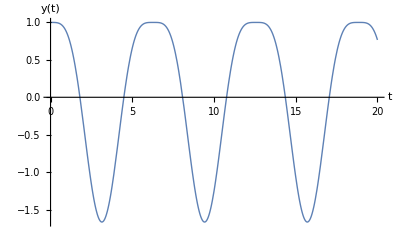

```mathematica
Plot[sol,{t,0,20},]
```

## Example 3: Nonhomogeneous Equation

Consider the differential equation:

y''(t)+2 y'(t)+5 y(t)=3 e^-t sin(t)

combined with the initial conditions:

y(0)=1

y'(0)=3

Define this equation in the Wolfram Language:

```mathematica
eqn=y''[t]+2y'[t]+5y[t]==3Exp[-t]Sin[t]
```

5 y[t]+2 y'[t]+y''[t]==3 ⅇ^-t Sin[t]

Use LaplaceTransform to transform the entire equation:

```mathematica
LaplaceTransform[eqn, t,s]
```

5 LaplaceTransform[y[t],t,s]+s^2 LaplaceTransform[y[t],t,s]+2 (s LaplaceTransform[y[t],t,s]-y[0])-s y[0]-y'[0]==3/(1+(1+s)^2)

## Example 3: Nonhomogeneous Equation

Substituting the initial conditions into the equation:

```mathematica
leqn = LaplaceTransform[eqn, t,s]/.{y[0]->1,y'[0]->3}
```

-3-s+5 LaplaceTransform[y[t],t,s]+s^2 LaplaceTransform[y[t],t,s]+2 (-1+s LaplaceTransform[y[t],t,s])==3/(1+(1+s)^2)

Solve for for L{y(t)}:

```mathematica
Solve[leqn,LaplaceTransform[y[t],t,s]]
```

{{LaplaceTransform[y[t],t,s]→(13+12 s+7 s^2+s^3)/((2+2 s+s^2) (5+2 s+s^2))}}

What you have found is that the solution to the initial value problem is the function that has the Laplace transform of:

F(s)=(13+12s+7 s^2+s^3)/((2+2s+s^2)(5+2s+s^2))

Thus you can solve for the unknown function using InverseLaplaceTransform.

## Example 3: Nonhomogeneous Equation

Find the solution using InverseLaplaceTransform:

```mathematica
InverseLaplaceTransform[(13+12 s+7 s^2+s^3)/((2+2 s+s^2) (5+2 s+s^2)),s,t]//ExpToTrig//FullSimplify
```

1/2 ⅇ^-t (2 (Cos[2 t]+Sin[t])+3 Sin[2 t])

You can confirm this result with the function DSolveValue:

```mathematica
sol=DSolveValue[{y''[t]+2y'[t]+5y[t]==3Exp[-t]Sin[t],y[0]==1,y'[0]==3},y[t],t]//FullSimplify
```

1/2 ⅇ^-t (2 (Cos[2 t]+Sin[t])+3 Sin[2 t])

Thus you have solved the initial value problem only using the Laplace transform and its associated properties:

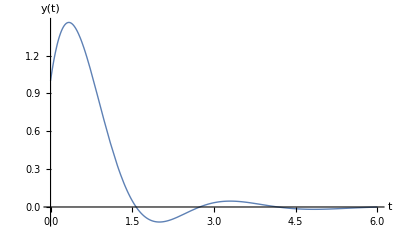

```mathematica
Plot[sol,{t,0,6},]
```

## Example 4: Nonhomogeneous Equation

Solve the initial value problem:

y''(t)+y(t)=3 t

y(0)=1

y'(0)=1

First, transform the equation into the equivalent equation in the s-domain:

```mathematica
leqn=LaplaceTransform[y''[t]+y[t]==3t, t,s]/.{y[0]->1,y'[0]->1}
```

-1-s+LaplaceTransform[y[t],t,s]+s^2 LaplaceTransform[y[t],t,s]==3/s^2

Next, solve for L{f(t)}:

```mathematica
Solve[leqn,LaplaceTransform[y[t],t,s]]
```

{{LaplaceTransform[y[t],t,s]→(3+s^2+s^3)/(s^2 (1+s^2))}}

Performing the InverseLaplaceTransform recovers the solution to the differential equation:

```mathematica
InverseLaplaceTransform[(3+s^2+s^3)/(s^2 (1+s^2)),s,t]
```

3 t+Cos[t]-2 Sin[t]

## Example 4: Nonhomogeneous Equation

You can confirm this result with the function DSolveValue:

```mathematica
sol=DSolveValue[{y''[t]+y[t]==3t,y[0]==1,y'[0]==1},y[t],t]//FullSimplify
```

3 t+Cos[t]-2 Sin[t]

The plot of the solution is shown here:

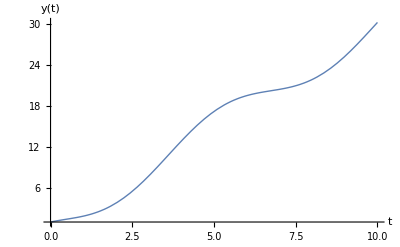

```mathematica
Plot[sol,{t,0,10},]
```

## Summary

This lesson explored an integral transform known as the LaplaceTransform:

L{f(t)}=F(s)=∫_0^∞ e^(-s t)f(t)ⅆt

You applied this transformation to differential equations and found that the transform reduced the equation to an algebraic equation that can be more easily solved.

After isolating the term L{f(t)}, the function f(t) can be found using the InverseLaplaceTransform.

With the Laplace transform, the solution methods for differential equations have been extensively improved.